## Harmonic Oscillator Potential

```mathematica
ClearAll["Global`*"]
```

Constants/Parameters

```mathematica
(*Constants (In Atomic Units)*)
m:=1
ℏ:=1
k:=1
ω:=√(m/k)

(*Parameters*)
L:=10
T:=10
fps:=60
numstates:=8
```

Definitions

```mathematica
(*Potential Energy*)
V[x_]:=1/2 m ω^2 x^2

(*Time Independent Schrodinger Equation*)
H=-ℏ^2/(2 m) ψ''[x]+V[x]*ψ[x];
```

Energy Eigenvalues/Eigenfunctions

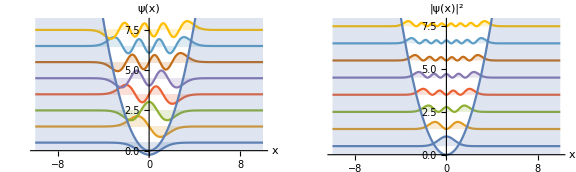

```mathematica
{vals,funs}=NDEigensystem[H,ψ[x],{x,-L,L},numstates,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.01}}}}];

(*Check Normalization*)
(*normfuns=Map[NIntegrate[#^2,{x,-L,L}]&,funs]*)
fillingrule:=Table[i->vals[[i]],{i,1,numstates}]
labels:=Table[ToString[Subscript[ψ, i],TraditionalForm],{i,1,numstates}]
title:=StringForm["Quantum Harmonic Oscillator: First `` Stationary States",numstates]

GraphicsRow[{Show[Plot[Evaluate[funs+vals],{x,-L,L},AxesLabel->{"x","ψ(x)"},Filling->fillingrule],Plot[V[x],{x,-L,L},Filling->Axis,Exclusions->None]],Show[Plot[Evaluate[funs^2+vals],{x,-L,L},AxesLabel->{"x","|ψ(x)|^2"},Filling->fillingrule],Plot[V[x],{x,-L,L},Filling->Axis,Exclusions->None]]},PlotLabel->title,ImageSize->Large]
```

Stationary States

```mathematica
ϵn[n_]:=Part[vals,n];
ψn[n_]:=Part[funs,n];
Ψn[n_]:=ψn[n] Exp[-ℏ ϵn[n] t/I];
```

Mixed State

```mathematica
(*ψ=ψn[1]+ψn[3]-ψn[4];
Ψ=Ψn[1]+Ψn[3]-Ψn[4];

norm=Sqrt[NIntegrate[(Conjugate[ψ] ψ),{x,-L,L}]];
Ψ=Ψ/norm;*)
```

```mathematica
(*animation:=Animate[Show[Plot[Evaluate[Conjugate[Ψ] Ψ]/.t->s,{x,-L,L},Axes->True,AxesLabel->{"x","|ψ(x)|^2"},PlotRange->{0,1},PlotStyle->Red],Plot[V[x],{x,-L,L},Filling->Axis,PlotStyle->Black,Exclusions->None]],{s,0,T},DisplayAllSteps->True,DefaultDuration->T];
animation*)
```